# Notebook for: Kantowski Sachs Taken From Gron

Geoff Cope
University of Utah
January 31, 2021

## Hyperlink To Book

```mathematica
Hyperlink["Einstein's General Theory of Relativity - With Modern Applications in Cosmology",
"https://www.springer.com/gp/book/9780387691992"]
```

[Einstein's General Theory of Relativity - With Modern Applications in Cosmology](https://www.springer.com/gp/book/9780387691992)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2 Kb

{Utilities`CleanSlate`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Line Element and Metric Derivation

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[eq15pt47]
eq15pt47  =
- dt^2+ a[t]^2 dz^2+ b[t]^2 ( dθ^2+ Sin[θ]^2 dϕ^2)
```

-dt^2+dz^2 a[t]^2+b[t]^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric15pt47]
metric15pt47 = 
lineToMetric[ eq15pt47 , {dt,dz,dθ,dϕ}] ;
metric15pt47 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a[t]^2 | 0 | 0
0 | 0 | b[t]^2 | 0
0 | 0 | 0 | b[t]^2 Sin[θ]^2)

```mathematica
Clear[inverse15pt47]
inverse15pt47 = 
Inverse[ metric15pt47 ]  ;
inverse15pt47 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1/a[t]^2 | 0 | 0
0 | 0 | 1/b[t]^2 | 0
0 | 0 | 0 | Csc[θ]^2/b[t]^2)

```mathematica
metric15pt47 . inverse15pt47 // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Tensors Calculated From Metric

```mathematica
$CacheTensorValues=True;
```

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ; 
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ;  
];
```

```mathematica
input[ "metric15pt47", metric15pt47, "KantowskiSachs","g^KS",{t,z,θ,ϕ},"Greek"] // Timing
```

{2.60098,Null}

```mathematica
TensorName[tensorList[[1]]]
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

KantowskiSachs

(-1 | 0 | 0 | 0
0 | (a(t))^2 | 0 | 0
0 | 0 | (b(t))^2 | 0
0 | 0 | 0 | (b(t))^2 sin^2(θ))

```mathematica
TensorName[tensorList[[2]]]
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

ChristoffelSymbolKantowskiSachs

((0
0
0
0) | (0
a(t) (∂a(t))/(∂t)
0
0) | (0
0
b(t) (∂b(t))/(∂t)
0) | (0
0
0
b(t) sin^2(θ) (∂b(t))/(∂t))
(0
((∂a(t))/(∂t))/(a(t))
0
0) | (((∂a(t))/(∂t))/(a(t))
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
((∂b(t))/(∂t))/(b(t))
0) | (0
0
0
0) | (((∂b(t))/(∂t))/(b(t))
0
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂b(t))/(∂t))/(b(t))) | (0
0
0
0) | (0
0
0
cot(θ)) | (((∂b(t))/(∂t))/(b(t))
0
cot(θ)
0))

```mathematica
TensorName[tensorList[[3]]]
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

RiemannTensorKantowskiSachs

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -a(t) (∂^2 a(t))/(∂t^2) | 0 | 0
a(t) (∂^2 a(t))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -b(t) (∂^2 b(t))/(∂t^2) | 0
0 | 0 | 0 | 0
b(t) (∂^2 b(t))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -b(t) sin^2(θ) (∂^2 b(t))/(∂t^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
b(t) sin^2(θ) (∂^2 b(t))/(∂t^2) | 0 | 0 | 0)
(0 | a(t) (∂^2 a(t))/(∂t^2) | 0 | 0
-a(t) (∂^2 a(t))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | a(t) b(t) (∂a(t))/(∂t) (∂b(t))/(∂t) | 0
0 | -a(t) b(t) (∂a(t))/(∂t) (∂b(t))/(∂t) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | a(t) b(t) sin^2(θ) (∂a(t))/(∂t) (∂b(t))/(∂t)
0 | 0 | 0 | 0
0 | -a(t) b(t) sin^2(θ) (∂a(t))/(∂t) (∂b(t))/(∂t) | 0 | 0)
(0 | 0 | b(t) (∂^2 b(t))/(∂t^2) | 0
0 | 0 | 0 | 0
-b(t) (∂^2 b(t))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -a(t) b(t) (∂a(t))/(∂t) (∂b(t))/(∂t) | 0
0 | a(t) b(t) (∂a(t))/(∂t) (∂b(t))/(∂t) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (b(t))^2 sin^2(θ) (((∂b(t))/(∂t))^2+1)
0 | 0 | -(b(t))^2 sin^2(θ) (((∂b(t))/(∂t))^2+1) | 0)
(0 | 0 | 0 | b(t) sin^2(θ) (∂^2 b(t))/(∂t^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-b(t) sin^2(θ) (∂^2 b(t))/(∂t^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -a(t) b(t) sin^2(θ) (∂a(t))/(∂t) (∂b(t))/(∂t)
0 | 0 | 0 | 0
0 | a(t) b(t) sin^2(θ) (∂a(t))/(∂t) (∂b(t))/(∂t) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(b(t))^2 sin^2(θ) (((∂b(t))/(∂t))^2+1)
0 | 0 | (b(t))^2 sin^2(θ) (((∂b(t))/(∂t))^2+1) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
TensorName[tensorList[[4]]]
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

RicciTensorKantowskiSachs

(-((∂^2 a(t))/(∂t^2))/(a(t))-(2 (∂^2 b(t))/(∂t^2))/(b(t)) | 0 | 0 | 0
0 | a(t) ((2 (∂a(t))/(∂t) (∂b(t))/(∂t))/(b(t))+(∂^2 a(t))/(∂t^2)) | 0 | 0
0 | 0 | (b(t) (∂a(t))/(∂t) (∂b(t))/(∂t))/(a(t))+b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1 | 0
0 | 0 | 0 | (sin^2(θ) (a(t) (b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)+b(t) (∂a(t))/(∂t) (∂b(t))/(∂t)))/(a(t)))

```mathematica
TensorName[tensorList[[5]]]
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

RicciScalarKantowskiSachs

(2 (b(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (2 b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(a(t) (b(t))^2)

```mathematica
TensorName[tensorList[[6]]]
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

KretschmannScalarKantowskiSachs

(8 ((((∂a(t))/(∂t))^2 ((∂b(t))/(∂t))^2)/(a(t))^2+((∂^2 b(t))/(∂t^2))^2))/(b(t))^2+(4 ((∂^2 a(t))/(∂t^2))^2)/(a(t))^2+(4 (((∂b(t))/(∂t))^2+1)^2)/(b(t))^4

```mathematica
TensorName[tensorList[[7]]]
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

EinsteinTensorKantowskiSachs

((a(t) ((∂b(t))/(∂t))^2+2 b(t) (∂a(t))/(∂t) (∂b(t))/(∂t)+a(t))/(a(t) (b(t))^2) | 0 | 0 | 0
0 | -((a(t))^2 (2 b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))/(b(t))^2 | 0 | 0
0 | 0 | -(b(t) (b(t) (∂^2 a(t))/(∂t^2)+a(t) (∂^2 b(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t)))/(a(t)) | 0
0 | 0 | 0 | -(b(t) sin^2(θ) (b(t) (∂^2 a(t))/(∂t^2)+a(t) (∂^2 b(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t)))/(a(t)))

```mathematica
TensorName[tensorList[[8]]]
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

WeylTensorKantowskiSachs

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (a(t) (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(3 (b(t))^2) | 0 | 0
(a(t) (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(3 (b(t))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))/(6 a(t)) | 0
0 | 0 | 0 | 0
(b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))/(6 a(t)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ) (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(6 a(t))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(6 a(t)) | 0 | 0 | 0)
(0 | (a(t) (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(3 (b(t))^2) | 0 | 0
(a(t) (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(3 (b(t))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/6 a(t) (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)) | 0
0 | 1/6 a(t) (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 a(t) sin^2(θ) (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))
0 | 0 | 0 | 0
0 | -1/6 a(t) sin^2(θ) (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)) | 0 | 0)
(0 | 0 | (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))/(6 a(t)) | 0
0 | 0 | 0 | 0
(b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))/(6 a(t)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/6 a(t) (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)) | 0
0 | 1/6 a(t) (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ((b(t))^2 sin^2(θ) (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(3 a(t))
0 | 0 | -((b(t))^2 sin^2(θ) (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(3 a(t)) | 0)
(0 | 0 | 0 | (sin^2(θ) (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(6 a(t))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(6 a(t)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -1/6 a(t) sin^2(θ) (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))
0 | 0 | 0 | 0
0 | 1/6 a(t) sin^2(θ) (b(t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))-a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -((b(t))^2 sin^2(θ) (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(3 a(t))
0 | 0 | ((b(t))^2 sin^2(θ) (b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)))/(3 a(t)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
TensorName[tensorList[[9]]]
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

CottonTensorKantowskiSachs

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
(2 ((a(t))^2 (-(-(b(t))^2 (∂^3 b(t))/(∂t^3)+((∂b(t))/(∂t))^3+(∂b(t))/(∂t)))+a(t) b(t) ((∂a(t))/(∂t) (b(t) (∂^2 b(t))/(∂t^2)+2 ((∂b(t))/(∂t))^2)-b(t) (b(t) (∂^3 a(t))/(∂t^3)+2 (∂^2 a(t))/(∂t^2) (∂b(t))/(∂t)))+(b(t))^2 (∂a(t))/(∂t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))))/(3 (b(t))^3)
0
0) | ((2 ((a(t))^2 (-(b(t))^2 (∂^3 b(t))/(∂t^3)+((∂b(t))/(∂t))^3+(∂b(t))/(∂t))+a(t) b(t) (b(t) (b(t) (∂^3 a(t))/(∂t^3)+2 (∂^2 a(t))/(∂t^2) (∂b(t))/(∂t))-(∂a(t))/(∂t) (b(t) (∂^2 b(t))/(∂t^2)+2 ((∂b(t))/(∂t))^2))+(b(t))^2 (∂a(t))/(∂t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))))/(3 (b(t))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
((a(t))^2 (-(b(t))^2 (∂^3 b(t))/(∂t^3)+((∂b(t))/(∂t))^3+(∂b(t))/(∂t))+a(t) b(t) (b(t) (b(t) (∂^3 a(t))/(∂t^3)+2 (∂^2 a(t))/(∂t^2) (∂b(t))/(∂t))-(∂a(t))/(∂t) (b(t) (∂^2 b(t))/(∂t^2)+2 ((∂b(t))/(∂t))^2))+(b(t))^2 (∂a(t))/(∂t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2)))/(3 (a(t))^2 b(t))
0) | (0
0
0
0) | (1/3 ((b(t) (∂a(t))/(∂t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t)))/(a(t))^2+((∂a(t))/(∂t) (b(t) (∂^2 b(t))/(∂t^2)+2 ((∂b(t))/(∂t))^2)-b(t) (b(t) (∂^3 a(t))/(∂t^3)+2 (∂^2 a(t))/(∂t^2) (∂b(t))/(∂t)))/(a(t))-(-(b(t))^2 (∂^3 b(t))/(∂t^3)+((∂b(t))/(∂t))^3+(∂b(t))/(∂t))/(b(t)))
0
0
0) | (0
0
0
0)
(0
0
0
(sin^2(θ) ((a(t))^2 (-(b(t))^2 (∂^3 b(t))/(∂t^3)+((∂b(t))/(∂t))^3+(∂b(t))/(∂t))+a(t) b(t) (b(t) (b(t) (∂^3 a(t))/(∂t^3)+2 (∂^2 a(t))/(∂t^2) (∂b(t))/(∂t))-(∂a(t))/(∂t) (b(t) (∂^2 b(t))/(∂t^2)+2 ((∂b(t))/(∂t))^2))+(b(t))^2 (∂a(t))/(∂t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))))/(3 (a(t))^2 b(t))) | (0
0
0
0) | (0
0
0
0) | (-(sin^2(θ) ((a(t))^2 (-(b(t))^2 (∂^3 b(t))/(∂t^3)+((∂b(t))/(∂t))^3+(∂b(t))/(∂t))+a(t) b(t) (b(t) (b(t) (∂^3 a(t))/(∂t^3)+2 (∂^2 a(t))/(∂t^2) (∂b(t))/(∂t))-(∂a(t))/(∂t) (b(t) (∂^2 b(t))/(∂t^2)+2 ((∂b(t))/(∂t))^2))+(b(t))^2 (∂a(t))/(∂t) ((∂a(t))/(∂t) (∂b(t))/(∂t)-b(t) (∂^2 a(t))/(∂t^2))))/(3 (a(t))^2 b(t))
0
0
0))

## Stress Energy Tensor Construction

```mathematica
TensorName[tensorList[[7]]]
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

EinsteinTensorKantowskiSachs

((a(t) ((∂b(t))/(∂t))^2+2 b(t) (∂a(t))/(∂t) (∂b(t))/(∂t)+a(t))/(a(t) (b(t))^2) | 0 | 0 | 0
0 | -((a(t))^2 (2 b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))/(b(t))^2 | 0 | 0
0 | 0 | -(b(t) (b(t) (∂^2 a(t))/(∂t^2)+a(t) (∂^2 b(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t)))/(a(t)) | 0
0 | 0 | 0 | -(b(t) sin^2(θ) (b(t) (∂^2 a(t))/(∂t^2)+a(t) (∂^2 b(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t)))/(a(t)))

```mathematica
Clear[kantowskiSachsSET]
kantowskiSachsSET = 
TensorValues[MultiplyTensorScalar[-Λ, tensorList[[1]]]]  ;
kantowskiSachsSET  // MatrixForm // pdConv
```

(Λ | 0 | 0 | 0
0 | -Λ (a(t))^2 | 0 | 0
0 | 0 | -Λ (b(t))^2 | 0
0 | 0 | 0 | -Λ (b(t))^2 sin^2(θ))

## Einstein Field Equations Derivation

```mathematica
Clear[eq15pt48a]
eq15pt48a =
Thread[
Table[ TensorValues[tensorList[[7]]][[i,i]],{i,1,4}] == 
Table[kantowskiSachsSET[[i,i]],{i,1,4}]] ;
eq15pt48a  // TableForm // pdConv
```

(a(t) ((∂b(t))/(∂t))^2+2 b(t) (∂a(t))/(∂t) (∂b(t))/(∂t)+a(t))/(a(t) (b(t))^2)==Λ
-((a(t))^2 (2 b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))/(b(t))^2==-Λ (a(t))^2
-(b(t) (b(t) (∂^2 a(t))/(∂t^2)+a(t) (∂^2 b(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t)))/(a(t))==-Λ (b(t))^2
-(b(t) sin^2(θ) (b(t) (∂^2 a(t))/(∂t^2)+a(t) (∂^2 b(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t)))/(a(t))==-Λ (b(t))^2 sin^2(θ)

```mathematica
eq15pt48a [[1]] // Apart
```

1/b[t]^2+(2 a'[t] b'[t])/(a[t] b[t])+b'[t]^2/b[t]^2==Λ

```mathematica
Assuming[ a[t]≠ 0 ,
DivideSides[eq15pt48a [[2]]  , -a[t]^2]] // Expand // Simplify
```

(1+b'[t]^2+2 b[t] b''[t])/b[t]^2==Λ

```mathematica
Assuming[ Λ ≠ 0 && b[t] ≠ 0 && a[t] ≠ 0 ,
DivideSides[
eq15pt48a [[3]]  , - b[t]^2] ] // Expand // Simplify // Apart
```

(a'[t] b'[t]+b[t] a''[t])/(a[t] b[t])+b''[t]/b[t]==Λ

```mathematica
Assuming[ Λ ≠ 0 && b[t] ≠ 0 && a[t] ≠ 0  &&  Sin[θ]≠ 0 ,
DivideSides[
eq15pt48a [[4]] , - b[t]^2 Sin[θ]^2 ]] // Expand // Simplify // Apart 
(* We recognize this as the same as above... *)
```

(a'[t] b'[t]+b[t] a''[t])/(a[t] b[t])+b''[t]/b[t]==Λ

```mathematica
Clear[eq15pt48]
eq15pt48 = {
eq15pt48a [[1]] // Apart  , 
Assuming[ a[t]≠ 0 ,
DivideSides[eq15pt48a [[2]]  , -a[t]^2]] // Expand // Simplify,
Assuming[ Λ ≠ 0 && b[t] ≠ 0 && a[t] ≠ 0 ,
DivideSides[
eq15pt48a [[3]]  , - b[t]^2] ] // Expand // Simplify // Apart 
} ;
eq15pt48  // TableForm // pdConv
```

(2 (∂a(t))/(∂t) (∂b(t))/(∂t))/(a(t) b(t))+1/(b(t))^2+((∂b(t))/(∂t))^2/(b(t))^2==Λ
(2 b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1)/(b(t))^2==Λ
(b(t) (∂^2 a(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t))/(a(t) b(t))+((∂^2 b(t))/(∂t^2))/(b(t))==Λ

## Dynamical Equations - Dynamical System

```mathematica
Clear[ics,b]
ics = { 
a[0] ==  1,
a'[0] == 1 , 
b[0] ==  1, 
b'[0] ==   1
} ;
ics // TableForm
```

a[0]==1
a'[0]==1
b[0]==1
b'[0]==1

```mathematica
Clear[kantowskiSachsODEs]
kantowskiSachsODEs = 
Union[(eq15pt48[[2;;3]]  /. Λ-> 1 ),ics]
```

{a[0]==1,b[0]==1,a'[0]==1,b'[0]==1,(a'[t] b'[t]+b[t] a''[t])/(a[t] b[t])+b''[t]/b[t]==1,(1+b'[t]^2+2 b[t] b''[t])/b[t]^2==1}

```mathematica
Clear[kantowskiSachsODEsolution]
kantowskiSachsODEsolution = 
Flatten[NDSolve[ kantowskiSachsODEs , {a[t],b[t]}, {t,0,1}]]
```

{a[t]→InterpolatingFunction[…][t],b[t]→InterpolatingFunction[…][t]}

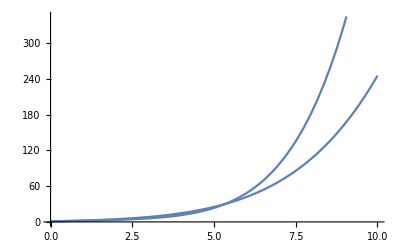

```mathematica
Plot[
{a[t],b[t]} /. kantowskiSachsODEsolution , {t,0,10}]
```

```mathematica
Clear[dynamic]

Manipulate[
dynamic = Module[{ics,kantowskiSachsODEsolution}, 
Clear[ics];
ics = { 
a[0] ==  a0,
a'[0] == va0 , 
b[0] ==  b0, 
b'[0] ==   vb0
} ;
Clear[kantowskiSachsODEs] ;
kantowskiSachsODEs = 
Union[(eq15pt48[[2;;3]]  /. Λ-> 1 ),ics] ;
Clear[kantowskiSachsODEsolution];
kantowskiSachsODEsolution = 
Flatten[NDSolve[ kantowskiSachsODEs , {a[t],b[t]}, {t,0,1}]] ;
Plot[
{a[t],b[t]} /. kantowskiSachsODEsolution , {t,0,10},
PlotRange-> {-600,600} , PlotLabel-> "Kantowski Sachs Scale Factors Gron Page 422",
 PlotLegends-> {a[t],b[t]}]
(* Not sure why not labelling b - go back and redo *) 
],
{a0,1,1.1},
{va0,1,1.1} ,
{b0,1,1.1},
{vb0,1,1.1}
]
```

## Null Tetrad Construction

```mathematica
Clear[ℓ]
ℓ =(1/(√2)) {PowerExpand[Sqrt[-metric15pt47[[1,1]]]] , PowerExpand[Sqrt[metric15pt47[[2,2]]]],0,0}
```

{1/(√2),a[t]/(√2),0,0}

```mathematica
Clear[𝓃]
𝓃 =(1/(√2))  {PowerExpand[Sqrt[-metric15pt47[[1,1]]]] , -PowerExpand[Sqrt[metric15pt47[[2,2]]]],0,0}
```

{1/(√2),-a[t]/(√2),0,0}

```mathematica
Clear[𝓂] 
𝓂 =(1/(√2))  {0,0,PowerExpand[Sqrt[metric15pt47[[3,3]]]],ⅈ PowerExpand[Sqrt[metric15pt47[[4,4]]]]}
```

{0,0,b[t]/(√2),(ⅈ b[t] Sin[θ])/(√2)}

```mathematica
Clear[𝓂bar]
𝓂bar =(1/(√2))  {0,0,PowerExpand[Sqrt[metric15pt47[[3,3]]]],-ⅈ PowerExpand[Sqrt[metric15pt47[[4,4]]]]}
```

{0,0,b[t]/(√2),-(ⅈ b[t] Sin[θ])/(√2)}

```mathematica
l = ToTensor[ {"NewTensor" , "l"} , tensorList[[1]] , ℓ , {-μ}]
n = ToTensor[{"NewTensor" , "n" } , tensorList[[1]] , 𝓃 , {-μ} ] 
m = ToTensor[{"NewTensor" , "m" } , tensorList[[1]] , 𝓂 , {-μ} ] 
mbar = ToTensor[{"NewTensor" , "mbar" } , tensorList[[1]] , 𝓂bar , {-μ} ]
```

l_μ^

n_μ^

m_μ^

mbar_μ^

```mathematica
TensorValues[ContractIndices[l[-μ]l[μ]]] == 0  // Expand // FullSimplify 
TensorValues[ContractIndices[n[-μ]n[μ]] ]== 0  // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]m[μ]]] == 0   // Expand // FullSimplify 
TensorValues[ContractIndices[mbar[-μ]mbar[μ]]] == 0  // Expand // FullSimplify 
TensorValues[ContractIndices[l[-μ]n[μ]]] == -1// Expand // FullSimplify 
TensorValues[ContractIndices[l[μ]n[-μ]]] ==- 1  // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]mbar[μ]]] ==  1 // Expand // FullSimplify 
TensorValues[ContractIndices[m[μ]mbar[-μ]]] ==  1 // Expand // FullSimplify 
Clear[completenessDownIndices]
completenessDownIndices = 
MergeTensors[-l[-μ]n[-ν]-n[-μ]l[-ν] + m[-μ]mbar[-ν]+ m[-ν]mbar[-μ]]  ;
TensorValues[ completenessDownIndices ]  // MatrixForm

Thread[Flatten[metric15pt47] == 
Flatten[ TensorValues[ completenessDownIndices ]] ] // Expand // FullSimplify 

Clear[completenessUpIndices]
completenessUpIndices = 
MergeTensors[-l[μ]n[ν]-n[μ]l[ν] + m[μ]mbar[ν]+ m[ν]mbar[μ]]  ;
TensorValues[ completenessUpIndices ]  // MatrixForm

Thread[Flatten[inverse15pt47] == 
Flatten[ TensorValues[ completenessUpIndices ]] ]  // Expand // FullSimplify
```

True

True

True

«5 more identical outputs»

(-1 | 0 | 0 | 0
0 | a[t]^2 | 0 | 0
0 | 0 | b[t]^2 | 0
0 | 0 | 0 | b[t]^2 Sin[θ]^2)

True

(-1 | 0 | 0 | 0
0 | 1/a[t]^2 | 0 | 0
0 | 0 | 1/b[t]^2 | 0
0 | 0 | 0 | Csc[θ]^2/b[t]^2)

True

## Calculation of Newman Penrose Quantities: Spin Coefficients , Ricci Scalars , Weyl Scalars

```mathematica
Clear[spinCoefficientReplace]  (* Page 56 Wang *) (* check where these definitions came from *)
spinCoefficientReplace= {
α-> ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ] mbar[ν]] // TensorValues )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] mbar[ν]] // TensorValues)) ) , 
β -> 
((1/2)((MergeTensors[ CovariantD[ l[-μ],-ν] n[μ]m[ν]] // TensorValues)- 
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] m[ν]] // TensorValues ))),
ρ ->(  MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] mbar[ν] ] // TensorValues  // Expand // FullSimplify )  , 
γ -> (* something weird here correct definition off by minus sign *) ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ]n[ν] ] // TensorValues  // Expand  )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] n[ν]] // TensorValues // Expand  // FullSimplify )) // Expand ) ,
ε -> ( (1/2)(( MergeTensors[CovariantD[l[-μ],-ν] n[μ] l[ν]] // TensorValues  // Expand  // FullSimplify  )  - 
(MergeTensors[ CovariantD[ m[-μ],-ν] mbar[μ] l[ν]] // TensorValues // Expand // FullSimplify) ) // Expand  // FullSimplify ) ,
κ->(  MergeTensors[ CovariantD[ l[-μ] ,-ν] m[μ] l[ν]  ]  // TensorValues ) ,
λ-> (* note minus sign *)(-1)*( MergeTensors[ CovariantD[ n[-μ],-ν] mbar[μ] mbar[ν] ]  // TensorValues // Expand // FullSimplify)  ,

μ-> (*note minus sign *)(-1)*( MergeTensors [ CovariantD[ n[-μ] , -ν ] mbar[μ] m[ν] ] // TensorValues  // Expand  // FullSimplify )  , 
ν-> ( MergeTensors[ CovariantD[ n[-μ],-ν]m[μ] n[ν] ] // TensorValues  // Expand) ,
 π-> (* Note minus sign *)(-1)* (MergeTensors[CovariantD[ n[-μ],-ν] mbar[μ] l[ν]] // TensorValues  // Expand ) , 
 ρ ->(  MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] mbar[ν] ] // TensorValues  // Expand // FullSimplify )  , 
σ->( MergeTensors[ CovariantD[l[-μ] , -ν] m[μ] m[ν]] // TensorValues  // Expand // FullSimplify)  , 
τ->( MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] n[ν ]]// TensorValues  // Expand ) 
} ;
spinCoefficientReplace // TableForm // pdConv
```

α→(cot(θ))/(2 √2 b(t))
β→-(cot(θ))/(2 √2 b(t))
ρ→-((∂b(t))/(∂t))/(√2 b(t))
γ→-((∂a(t))/(∂t))/(2 √2 a(t))
ε→((∂a(t))/(∂t))/(2 √2 a(t))
κ→0
λ→0
μ→((∂b(t))/(∂t))/(√2 b(t))
ν→0
π→0
ρ→-((∂b(t))/(∂t))/(√2 b(t))
σ→0
τ→0

```mathematica
Clear[ricciScalarsReplace] (* Definitions from Griffiths *) 
ricciScalarsReplace = {
Subscript[Φ, oo]-> (* be careful about oh's not zeros *) 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]l[ν]]] // Expand // FullSimplify  , 
Subscript[Φ, O1]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, O2]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, 11]-> 
(-1/4)*( ( TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]n[ν]]])+ (TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]mbar[ν]]])) // Expand // FullSimplify, 
Subscript[Φ, 12]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, 22]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]n[ν]]]// Expand // FullSimplify , 
 Λ-> 
(1/24)*TensorValues[tensorList[[5]]]// Expand // FullSimplify 
} ;
ricciScalarsReplace  // TableForm // pdConv
```

Φ_oo→(a(t) (∂^2 b(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))/(2 a(t) b(t))
Φ_O1→0
Φ_O2→0
Φ_11→1/4 (((∂^2 a(t))/(∂t^2))/(a(t))-(((∂b(t))/(∂t))^2+1)/(b(t))^2)
Φ_12→0
Φ_22→(a(t) (∂^2 b(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))/(2 a(t) b(t))
Λ→(b(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (2 b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))/(12 a(t) (b(t))^2)

```mathematica
Clear[weylScalarsReplace](* Definitions from Griffiths *) 
weylScalarsReplace = {

Subscript[Ψ, 0]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 1]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]n[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 2]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]mbar[μ]n[ν]]] // Expand // FullSimplify, 
Subscript[Ψ, 3]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]l[λ]n[μ]mbar[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 4]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]mbar[λ]n[μ]mbar[ν]]]// Expand // FullSimplify
} ;
weylScalarsReplace // TableForm // pdConv
```

Ψ_0→0
Ψ_1→0
Ψ_2→(b(t) (b(t) (∂^2 a(t))/(∂t^2)-(∂a(t))/(∂t) (∂b(t))/(∂t))+a(t) (-b(t) (∂^2 b(t))/(∂t^2)+((∂b(t))/(∂t))^2+1))/(6 a(t) (b(t))^2)
Ψ_3→0
Ψ_4→0

```mathematica
weylScalarsReplace [[3]] // pdConv
```

Ψ_2→(b[t] (-a'[t] b'[t]+b[t] a''[t])+a[t] (1+b'[t]^2-b[t] b''[t]))/(6 a[t] b[t]^2)

```mathematica
weylScalarsReplace [[3,2]] // pdConv
```

(b[t] (-a'[t] b'[t]+b[t] a''[t])+a[t] (1+b'[t]^2-b[t] b''[t]))/(6 a[t] b[t]^2)

## Export Data Files For Use by xAct

CHECK THIS AND REDO
There should be an even faster way to do this with pipes if there are two kernels running

```mathematica
Put[Table[spinCoefficientReplace[[i,2]] , {i, 1, Length[spinCoefficientReplace]}],LocalObject["spinCoefficientReplace.nb"]]
```

LocalObject[file:///Users/geoffcope/Library/Wolfram/Objects/spinCoefficientReplace.nb]

```mathematica
Put[Table[spinCoefficientConjugateReplace[[i,2]] , {i, 1, Length[spinCoefficientReplace]}], LocalObject["spinCoefficientConjugateReplace.nb"]]
```

LocalObject[file:///Users/geoffcope/Library/Wolfram/Objects/spinCoefficientConjugateReplace.nb]

```mathematica
Put[Table[ricciScalarsReplace[[i,2]] , {i, 1, Length[ricciScalarsReplace]}],LocalObject["ricciScalarsReplace.nb"] ]
```

LocalObject[file:///Users/geoffcope/Library/Wolfram/Objects/ricciScalarsReplace.nb]

```mathematica
Put[Table[weylScalarsReplace[[i,2]] , {i, 1, Length[weylScalarsReplace]}],LocalObject["weylScalarsReplace.nb"] ]
```

LocalObject[file:///Users/geoffcope/Library/Wolfram/Objects/weylScalarsReplace.nb]

## Test Importing Files Back In

```mathematica
Clear[testa]
testa = 
Get[LocalObject["spinCoefficientReplace.nb"]]

Clear[testb]
testb  = 
Get[LocalObject["spinCoefficientConjugateReplace.nb"]]

Clear[testc]
testc = 
Get[LocalObject["ricciScalarsReplace.nb"]]

Clear[testd]
testd = 
Get[LocalObject["weylScalarsReplace.nb"] ]
```

{0,0,1/2 ⅇ^(-M[u,v]) A[u,v]^2 B^(1,0)[u,v]-1/4 ⅈ A[u,v] Sinh[W[u,v]] V^(1,0)[u,v],1/4 B[u,v] (2 ⅇ^(-M[u,v]) A[u,v] (B^(0,1)[u,v]-B[u,v] M^(0,1)[u,v])-ⅈ Sinh[W[u,v]] V^(0,1)[u,v]),0,1/2 A[u,v] (Cosh[W[u,v]] V^(1,0)[u,v]+ⅈ W^(1,0)[u,v]),-1/2 A[u,v] U^(1,0)[u,v],0,0,1/2 B[u,v] U^(0,1)[u,v],-1/2 B[u,v] (Cosh[W[u,v]] V^(0,1)[u,v]-ⅈ W^(0,1)[u,v]),0}

{0,0,1/2 ⅇ^(-M[u,v]) A[u,v]^2 B^(1,0)[u,v]+1/4 ⅈ A[u,v] Sinh[W[u,v]] V^(1,0)[u,v],1/4 B[u,v] (2 ⅇ^(-M[u,v]) A[u,v] (B^(0,1)[u,v]-B[u,v] M^(0,1)[u,v])+ⅈ Sinh[W[u,v]] V^(0,1)[u,v]),0,1/2 A[u,v] (Cosh[W[u,v]] V^(1,0)[u,v]-ⅈ W^(1,0)[u,v]),-1/2 A[u,v] U^(1,0)[u,v],0,0,1/2 B[u,v] U^(0,1)[u,v],-1/2 B[u,v] (Cosh[W[u,v]] V^(0,1)[u,v]+ⅈ W^(0,1)[u,v]),0}

{1/4 B[u,v]^2 (-2 M^(0,1)[u,v] U^(0,1)[u,v]+(U^(0,1)[u,v])^2+Cosh[W[u,v]]^2 (V^(0,1)[u,v])^2+(W^(0,1)[u,v])^2-2 U^(0,2)[u,v]),0,1/4 ⅇ^M[u,v] (W^(0,1)[u,v] (-ⅈ U^(1,0)[u,v]-2 Sinh[W[u,v]] V^(1,0)[u,v])+U^(0,1)[u,v] (Cosh[W[u,v]] V^(1,0)[u,v]-ⅈ W^(1,0)[u,v])+V^(0,1)[u,v] (Cosh[W[u,v]] U^(1,0)[u,v]-ⅈ Sinh[2 W[u,v]] V^(1,0)[u,v]-2 Sinh[W[u,v]] W^(1,0)[u,v])-2 Cosh[W[u,v]] V^(1,1)[u,v]+2 ⅈ W^(1,1)[u,v]),0,1/8 (-2 ⅇ^M[u,v] (U^(0,1)[u,v] U^(1,0)[u,v]-U^(1,1)[u,v])+A[u,v] B[u,v] (U^(0,1)[u,v] U^(1,0)[u,v]+Cosh[W[u,v]]^2 V^(0,1)[u,v] V^(1,0)[u,v]+W^(0,1)[u,v] W^(1,0)[u,v]-2 (M^(1,1)[u,v]+U^(1,1)[u,v]))),0,1/4 ⅇ^M[u,v] (Cosh[W[u,v]] U^(0,1)[u,v] V^(1,0)[u,v]+W^(0,1)[u,v] (ⅈ U^(1,0)[u,v]-2 Sinh[W[u,v]] V^(1,0)[u,v])+ⅈ U^(0,1)[u,v] W^(1,0)[u,v]+V^(0,1)[u,v] (Cosh[W[u,v]] U^(1,0)[u,v]+ⅈ Sinh[2 W[u,v]] V^(1,0)[u,v]-2 Sinh[W[u,v]] W^(1,0)[u,v])-2 Cosh[W[u,v]] V^(1,1)[u,v]-2 ⅈ W^(1,1)[u,v]),0,1/4 A[u,v]^2 (-2 M^(1,0)[u,v] U^(1,0)[u,v]+(U^(1,0)[u,v])^2+Cosh[W[u,v]]^2 (V^(1,0)[u,v])^2+(W^(1,0)[u,v])^2-2 U^(2,0)[u,v]),-1/24 ⅇ^M[u,v] (3 U^(0,1)[u,v] U^(1,0)[u,v]+Cosh[W[u,v]]^2 V^(0,1)[u,v] V^(1,0)[u,v]+W^(0,1)[u,v] W^(1,0)[u,v]-2 M^(1,1)[u,v]-4 U^(1,1)[u,v])}

{1/4 B[u,v]^2 (-ⅈ Sinh[2 W[u,v]] (V^(0,1)[u,v])^2-4 Sinh[W[u,v]] V^(0,1)[u,v] W^(0,1)[u,v]-2 Cosh[W[u,v]] ((M^(0,1)[u,v]-U^(0,1)[u,v]) V^(0,1)[u,v]+V^(0,2)[u,v])+2 ⅈ ((M^(0,1)[u,v]-U^(0,1)[u,v]) W^(0,1)[u,v]+W^(0,2)[u,v])),0,1/12 A[u,v] B[u,v] (Cosh[W[u,v]] V^(0,1)[u,v] (2 Cosh[W[u,v]] V^(1,0)[u,v]+3 ⅈ W^(1,0)[u,v])+W^(0,1)[u,v] (-3 ⅈ Cosh[W[u,v]] V^(1,0)[u,v]+2 W^(1,0)[u,v])+2 (M^(1,1)[u,v]-U^(1,1)[u,v])),0,1/4 A[u,v]^2 (ⅈ Sinh[2 W[u,v]] (V^(1,0)[u,v])^2-4 Sinh[W[u,v]] V^(1,0)[u,v] W^(1,0)[u,v]-2 Cosh[W[u,v]] ((M^(1,0)[u,v]-U^(1,0)[u,v]) V^(1,0)[u,v]+V^(2,0)[u,v])-2 ⅈ ((M^(1,0)[u,v]-U^(1,0)[u,v]) W^(1,0)[u,v]+W^(2,0)[u,v]))}